```mathematica
Outline
-Decompose a polyhedron into its vertices 
-Make a function to generate a graph for the dual polyhedron
-Transform the polyhedron using rotation and translation so that one face is touching the ground
-Rotate and translate each adjacent face so that they are touching the ground
-Order them using the branches of the spanning tree of the graph 
-Create all possible nets from that
-Check for overlaps and delete those
-Return one random valid net
```

```mathematica
polyhedronfacegraph[polyhedron_]:= 
Block[{dualpolyhedron, vertexlist, vertexpairings, sortedvertices},

	 dualpolyhedron = DualPolyhedron[polyhedron];
     vertexlist = dualpolyhedron[[2]];
     
     vertexpairings = Flatten[
     Table[
     Append[
     Partition[vertexlist[[n]], 2, 1],
     {Last[vertexlist[[n]]],First[vertexlist[[n]]]}],
     {n, 1, Length[vertexlist]}], 
     1];
     
     sortedvertices = Sort /@ vertexpairings // DeleteDuplicates;

Graph[UndirectedEdge@@@sortedvertices,VertexLabels -> "Name"]
]
```

```mathematica
normvector[coords_] :=
Cross[coords[[2]] - coords[[1]], coords[[3]] - coords[[1]]];
```

```mathematica
extractfaces[polyhedron_] :=
Block[{transform,coordinatelist,vertexassoc,edgeassoc,coordinategroups,vertexlist,transformedvertices,polygoncoords},

coordinatelist = polyhedron[[1]];
vertexlist = polyhedron[[2]];

vertexassoc = Merge[Join@Table[<|n -> coordinatelist[[n]]|>, {n, 1, Length[coordinatelist]}],Total];
coordinategroups = Table[vertexassoc /@ vertexlist[[n]], {n, 1, Length[vertexlist]}];
edgeassoc = Merge[Join@Table[<|n -> EdgeList[polyhedronfacegraph@polyhedron][[n]]|>,
{n,1,Length[EdgeList[polyhedronfacegraph@polyhedron]]}],Total];

transform[n_] := 
N@RotationTransform[{normvector[coordinategroups[[n]]], {0,0,-1}}, Mean[coordinategroups[[n]]]];

transformedvertices = Table[transform[n]@coordinategroups[[n]],{n, 1, Length[coordinategroups]}];

polygoncoords = Table[Delete[transformedvertices[[n, m]],{3}],{n, 1, Length[transformedvertices]}, {m, 1, 3}];

Table[Graphics[Polygon[polygoncoords[[n]]]], {n,1,Length[polygoncoords]}]
]
```

```mathematica
(* rotationtransform[referenceface_,meshlist_]:= 
RotationTransform[{normvector[meshlist[[referenceface]][[1]]],{0, 0, -1}}, Mean[meshlist[[referenceface]][[1]]]];

translationtransform[mesh_] := 
TranslationTransform[-PropertyValue[{mesh, {2,1}}, MeshCellCentroid]];

replacemesh[referenceface_,n_,meshes_] := 
ReplacePart[meshes, n -> translationtransform[referenceface, meshes, meshes[[n]]]]; 

transformedmesh = rotationtransform[4, meshlist]/@ translationtransform[mesh]/@ meshlist;

 transformedmesh2 = ReplacePart[transformedmesh, 1 -> 
rotationtransform[1, transformedmesh]/@translationtransform[mesh]/@transformedmesh[[1]]]; 

Graphics3D[transformedmesh, Axes->True]
*)
```

```mathematica
ClearAll[generatenetcoords];

generatenetcoords[mesh_, tree_]:=
	Block[{transformations, transformedmesh, meshlist, transformedmeshlist, normals, polygonfaces, transformedrotation},
		polygonfaces = Reap[
		
		    meshlist = MeshPrimitives[mesh, 2][[All, 1]];
		    
			transformations = 
			RotationTransform[{normvector[meshlist[[1]]], {0, 0, -1}}] @*
			TranslationTransform[-PropertyValue[{mesh, {2, 1}}, MeshCellCentroid]];
			
			transformedmesh = TransformedRegion[mesh, transformations];
			
			transformedmeshlist = MeshPrimitives[transformedmesh, 2][[All, 1]];
			
			normals = normvector[#] &/@ transformedmeshlist;

			Sow[transformedmeshlist[[1]], "flat"];
			
			transformedrotation[1] = TransformationFunction[IdentityMatrix[4]];
			
			BreadthFirstScan[tree, 1, "DiscoverVertex" -> unfold[transformedmeshlist, normals, transformedrotation]];,
			{"flat"}
		][[-1, All, 1]];
		Chop[polygonfaces]
	]
	
	ClearAll[unfold];

unfold[meshlist_, normals_, transformedrotation_][u_, v_, _] /; (u =!= v) :=

	Block[{edgecoord1, edgecoord2, angle, rotation},
		{edgecoord1, edgecoord2} = Intersection @@ meshlist⟦{u, v}⟧; 
		angle = DihedralAngle[{edgecoord1, edgecoord2}, normals⟦{u, v}⟧];
		rotation = RotationTransform[angle, edgecoord2 - edgecoord1, Mean[{edgecoord1, edgecoord2}]];
		transformedrotation[u] = transformedrotation[v]@*rotation;
		Sow[transformedrotation[u] @ meshlist⟦u⟧, "flat"];
	]
```

```mathematica
generatetrees[graph_] := DeleteDuplicates[Table[FindSpanningTree[{graph, n}], {n ,1 , VertexCount[graph]}]]
```

```mathematica
ClearAll[generateallnets];

generateallnets[polyhedron_] := 
Block[{netcoords, trees, graph, mesh, surfacearea, netsurfacearea, goodnets},

mesh = BoundaryDiscretizeGraphics[polyhedron]; 
graph = polyhedronfacegraph[polyhedron];
trees = generatetrees[graph];

goodnets = {};

Table[

netcoords = First@generatenetcoords[mesh, trees[[treeposition]]];
netcoords = Table[Delete[netcoords[[n, m]], {3}], {n, 1, Length[netcoords]}, {m, 1, 3}];

surfacearea = SurfaceArea[polyhedron];
netsurfacearea = RegionMeasure[RegionUnion[Polygon /@ netcoords]];

If[surfacearea == netsurfacearea,
AppendTo[goodnets, Graphics[{Hue[0.94, 0.22, 1.], EdgeForm[{Thin, Pink}], Polygon /@ netcoords}]]
];, 

{treeposition, 1, Length[trees]}];

Row[{Graphics3D[polyhedron], goodnets}]

]
```

```mathematica
ClearAll[generateunconstrainednets];

generateunconstrainednets[polyhedron_] := 
Block[{netcoords, trees, graph, mesh, surfacearea, netsurfacearea, goodnets},

mesh = BoundaryDiscretizeGraphics[polyhedron]; 
graph = polyhedronfacegraph[polyhedron];
trees = generatetrees[graph];
goodnets = {};

Table[
netcoords = First@generatenetcoords[mesh, trees[[treeposition]]];
netcoords = Table[Delete[netcoords[[n, m]], {3}], {n, 1, Length[netcoords]}, {m, 1, 3}];

AppendTo[goodnets, Graphics[{Hue[0.94, 0.22, 1.], EdgeForm[{Thin, Pink}], Polygon /@ netcoords}]];,

{treeposition, 1, Length[trees]}];
goodnets]
```

```mathematica
sunny = RandomPolyhedron[{"ConvexHull",60}]
```

Polyhedron[…]

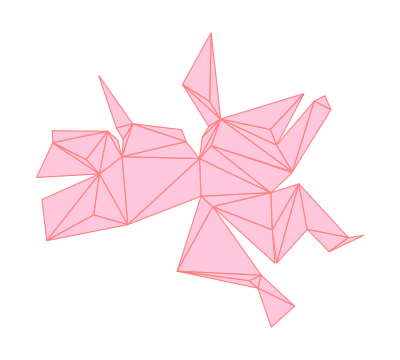
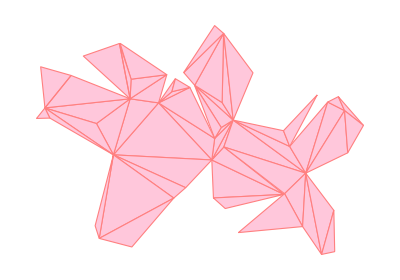
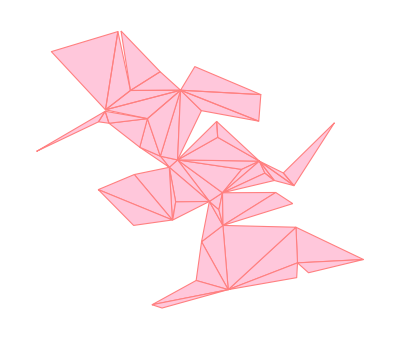
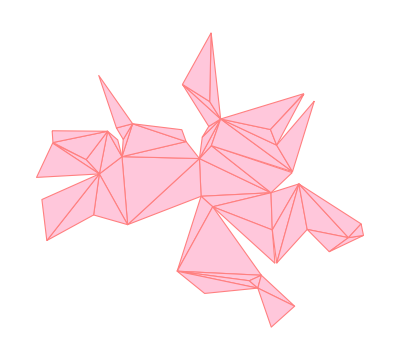
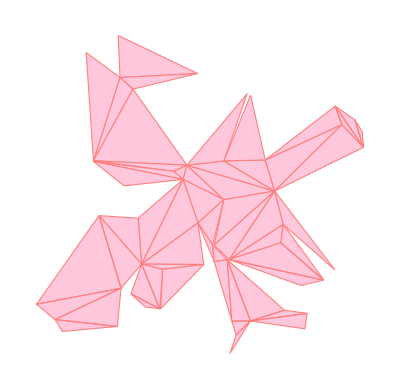
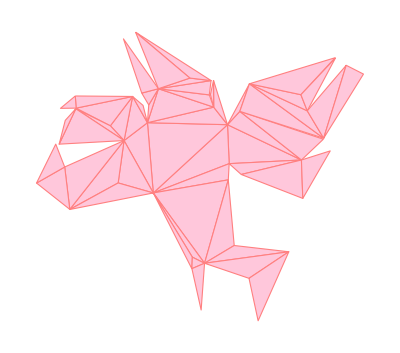
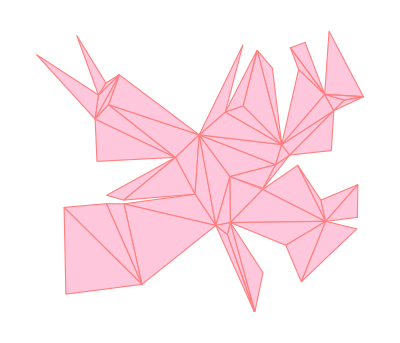
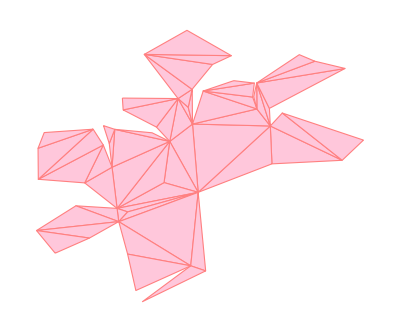

```mathematica
generateunconstrainednets[sunny]
```

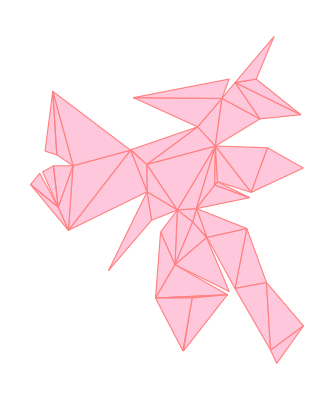
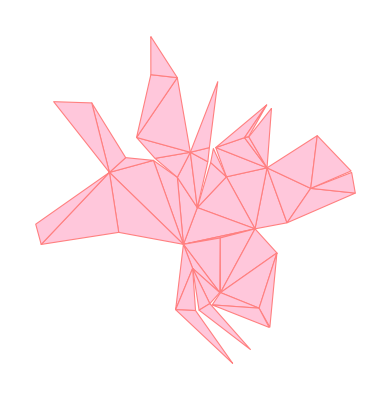
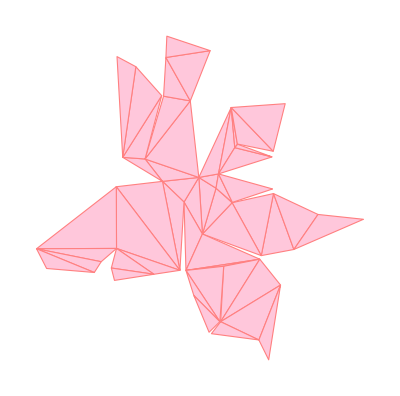
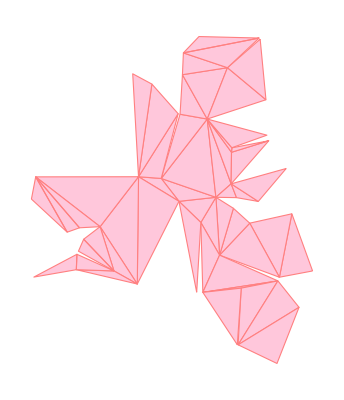
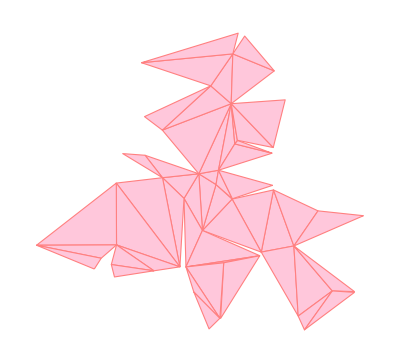
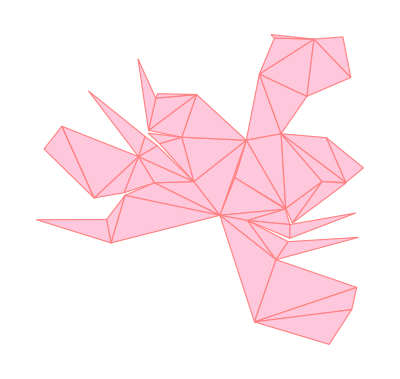
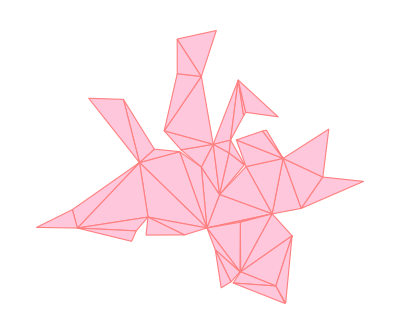
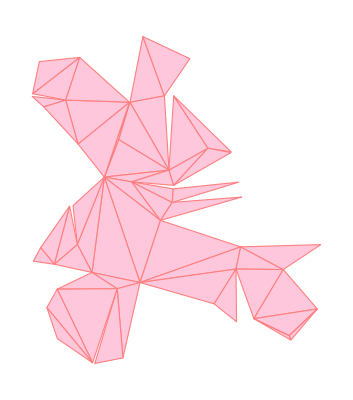
-Graphics3D-{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
generateallnets[sunny]
```

```mathematica
FeatureSpacePlot[%]
```

-Graphics-

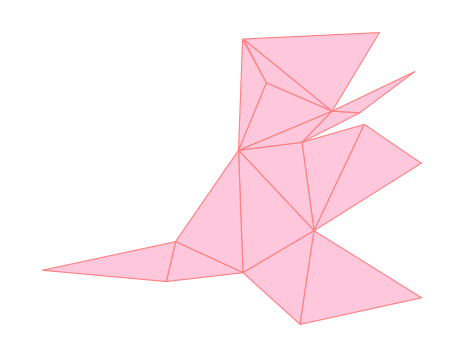
```mathematica
Rasterize@-Graphics-
```

-Graphics-

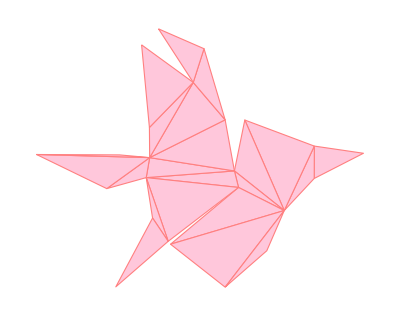

-Graphics-